```mathematica
Clear["Global`*"]
Needs["GallifreyanLetters`"]
(*
getSpacing[word_]:=chooseSpacing[#]&/@StringPartition[word//ToUpperCase,1];
getWordSize[word_]:=If[StringLength[word]<5,1,Total[getSpacing[word]]/(2Pi)];
centerPoint1[x_]:=If[StringLength[word]<5,.54,0.8253195827576976-0.11060277353478278 x+0.007703034792707071 x^2-0.00026579896491144955 x^3+3.570865399323157*^-6 x^4];
*)

Clear["Global`*"]
Needs["GallifreyanLetters`"]
wordPosition={0,0};
wordSize=1;
letterSize=0.2;
isVowelAfterConsonant[list_,pos_]:=If[isVowel[list[[pos]]]&&!isVowel[list[[pos-1]]]&&pos≠1,True,False];
hasLines[l_]:=If[l=="F"||l=="G"||l=="H"||l=="M"||l=="N"||l=="P"||l=="S"||l=="V"||l=="W"||l=="NG"||l=="QU"||l=="X"||l=="I"||l=="U",True,False];


(* Functions to measure length and postion *)
countLetterPositions[list_]:={For[i=1;pCounter=0,i≤ Length[list],i++,
If[!isVowelAfterConsonant[list,i],pCounter++,Nothing];
];pCounter}[[1]];
(* end *)

(* Functions for calculating edge points on word circle*)
edgePoint[offset_,rA_,rB_]:=(1-rB/rA)offset;
edgePoints[edgeInfo_,centerL_,radiusW_,radiusL_]:= edgeInfo[[1]][centerL]+edgePoint[edgeInfo[[2]],radiusW,radiusL]*{1,-1};
fixRightEdge[edge_]:=If[edge[[2]]≥0,edge,edge+{0,2Pi}];
fixLeftEdge[edge_]:=If[(edge[[1]]-edge[[2]])≤ 2Pi,edge,edge-{2Pi,0}];
addCircleIfNoEdges[edges_]:=If[Length[edges]==0,{{0,2Pi}},edges];
preAdjustEdges[edges_]:=If[Length[edges]==1,edges,fixRightEdge[#]&/@edges];
sortEdges[edges_]:=Partition[Insert[TakeDrop[edges,1][[1]]//Flatten,Reverse[TakeDrop[edges,1][[2]]//Flatten],-2]//Flatten,2];
postAdjustEdges[edges_]:=If[Length[edges]==1,edges,fixLeftEdge[#]&/@edges];
placeOnWord[edges_]:=Circle[wordPosition,wordSize,#]&/@edges;
formatEdges[edges_]:=placeOnWord[postAdjustEdges[sortEdges[preAdjustEdges[addCircleIfNoEdges[edges]]]]];
(* end *)

(* Functions to translate input string to Gallifreyan*)
isPairedLetter[string_]:=If[string=="CH"||string=="SH"||string=="TH"||string=="NG"||string=="QU",True,False];
take1[word_]:=StringTake[word,1];
take2[word_]:=StringTake[word,2];
drop1[word_]:=StringDrop[word,1];
drop2[word_]:=StringDrop[word,2];
stringParter[word_]:=If[isPairedLetter[If[StringLength[word]>1,take2[word],word]],take2[word],take1[word]];
stringDroper[word_]:=If[isPairedLetter[If[StringLength[word]>1,take2[word],word]],drop2[word],drop1[word]];
partitionInput[word_]:={For[i=0;mWord=word;result={},i<StringLength[word],i++,
If[mWord≠"",
AppendTo[result,stringParter[mWord]];
mWord=stringDroper[mWord];,
Nothing]
];result}//Flatten;
convertC[l_]:=If[l=="C","K",l];
(*
combinePairs[word_]:=partitionInput[word]
*)
convertToGallifreyan[word_]:=convertC/@partitionInput[word];
lettersList[word_]:=convertToGallifreyan[word];
convertLetters[list_]:=chooseLetter/@list;
convertEdges[list_]:=chooseEdge/@list;
convertLinePoints[list_]:=chooseLinePoints/@list;
(* end *)

(* Functions to place letters, edges, & lines on word circle *)
letterPositions[numOfPositions_]:=CirclePoints[wordPosition,{wordSize,(3Pi)/2},numOfPositions];
letterPositionsList[list_]:={For[numPos=countLetterPositions[list];i=1;pCounter=0;result={};,i≤Length[list],i++,
AppendTo[result,letterPositions[numPos][[If[isVowelAfterConsonant[list,i],pCounter,++pCounter]]]]
];result}[[1]];
edgeList[list_]:={For[mEdges=convertEdges[list];i=1;result={};,i≤Length[list],i++,
AppendTo[result,If[isVowelAfterConsonant[list,i],Nothing,mEdges  [[i]]   ]]
];result}[[1]];
linePointsPositionList[list_]:=If[hasLines[#[[1]]],#[[2]],Nothing]&/@Partition[Riffle[list,letterPositionsList[list]],2]

lettersOutput[list_]:=Partition[Riffle[convertLetters[list],letterPositionsList[list]],2];
edgesOutput[list_]:=Partition[Riffle[edgeList[list],letterPositions[countLetterPositions[list]]],2];
linePointsOutput[list_]:=Partition[Riffle[convertLinePoints[list],linePointsPositionList[list]],2];
(* end *)

(* Functions for printing letters, edges, & lines *)
printLetter[letter_,pos_]:=letter[pos,letterSize];
letters[list_]:=printLetter[#[[1]],#[[2]]]&/@lettersOutput[list];
printEdges[list_]:=edgePoints[#[[1]],#[[2]],wordSize,letterSize]&/@edgesOutput[list];
edges[list_]:=formatEdges[printEdges[list]];
printLinePoints[line_,pos_]:=line[pos,letterSize];
linePoints[list_]:=printLinePoints[#[[1]],#[[2]]]&/@linePointsOutput[list];
(* end *)

(* Functions for translating Gallifreyan *)
translateWordToGallifreyan[string_]:={mLetters=lettersList[string//ToUpperCase];
Graphics[{letters[mLetters],edges[mLetters]},
ImageSize->150]}[[1]];
(*
translateToGallifreyan[string_]:=RowBox[Riffle[translateWordToGallifreyan/@StringSplit[string],Spacer[20]]]//DisplayForm;
*)
translateToGallifreyan[string_]:=translateWordToGallifreyan/@StringSplit[string];
(* end *)

(* Functions for displays Gallifreyan text *)
circularTranslate[graphic_,radius_,sizeWeights_]:=Scale[Translate[#[[1,1]],#[[2]]],#[[3]]]&/@
Partition[Append[Riffle[Riffle[graphic,CirclePoints[{radius,(3Pi)/2},Length[graphic]]],sizeWeights,3],Last[sizeWeights]],3];

(* end *)
aWord="JAWAD HERE";
wordSizeWeights[sentence_] :=(StringLength/@StringSplit[sentence]//Normalize)+.3;
Rlength = 1.5;
aa=translateToGallifreyan[aWord];
ab=wordSizeWeights[aWord];
bb=circularTranslate[aa,Rlength,ab];
Graphics[{Circle[{0,0},2.5],bb}]

(*
linePointsOutput[lettersList[aWord]]//N;
linePoints[lettersList[aWord]];
*)

(* 
Connect lines if:
-directly opposite each other (abs[{x1,y1}] == abs[{x2,y2}]);
  -don't connect lines at same position on word circle;
  -letter has 2/more lines and next to another letter with 2/more lines
*)
```

-Graphics-

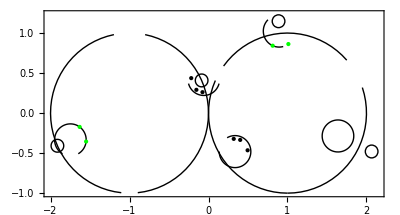

```mathematica
circularRotate[graphics_,angles_]:=GeometricTransformation[#[[1,1]],RotationTransform[#[[2]]]]&/@Partition[Riffle[graphics,angles],2];

a1=Translate[a1,{1,0}];
a2=Translate[a2,{-1,0}];
Graphics[{a1,a2},Frame->True]
```